```mathematica
Solve[((8.8139*10^(31)+x-5.4997*10^(31)-y*7.416*10^(15)*I)/(x-5.4997*10^(31)-y*7.416*10^(15)*I))^2/(8.8542*10^(-12))^2==2.116857^2&&((8.8139*10^(31)+x-3.47822*10^(30)-y*1.865*10^(15)*I))^2/(x-3.47822*10^(30)-y*1.865*10^(15)*I)^2/(8.8542*10^(-12))^2==1.8817136^2,{x,y}]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{x→-1.0197×10^32,y→0.+9.28099×10^15 ⅈ},{x→-1.0197×10^32,y→0.+9.28099×10^15 ⅈ},{x→-1.0197×10^32,y→0.+9.28099×10^15 ⅈ},{x→-1.0197×10^32,y→0.+9.28099×10^15 ⅈ}}

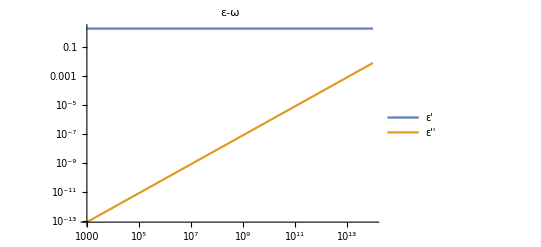

```mathematica
LogLogPlot[{1+(8.8139*10^(31)(1.0197*10^(32)-w^2))/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2),(8.8139*10^(31)*9.28*10^(15)*w)/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2)},{w,10^3,10^14},PlotLegends->{"ε'","ε''"},PlotLabel->"ε-ω"]
```

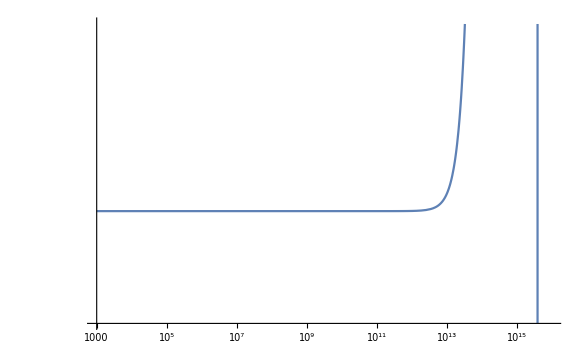

```mathematica
LogLogPlot[1+(8.8139*10^(31)(1.0197*10^(32)-w^2))/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2),{w,10^3,10^16}]
```

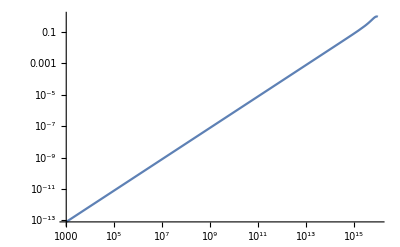

```mathematica
LogLogPlot[(8.8139*10^(31)*9.28*10^(15)*w)/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2),{w,10^3,10^16}]
```

```mathematica
LogLogPlot[{1+(8.8139*10^(31)(1.0197*10^(32)-w^2))/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2),(8.8139*10^(31)*9.28*10^(15)*w)/((1.0197*10^(32)-w^2)^2+(9.28*10^(15)*w)^2)},{w,10^3,10^14},PlotLegends->{"ε'","ε''"},PlotLabel->"ε-ω"]
```